```mathematica
β[ω_,δ_,t_,ϵ_]:=
β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[14],Join[Table[{i,i-1},{i,Range[2,14,1]}],Table[{i,i+1},{i,Range[1,14,1]}],Table[{2n-1,14-2n+2},{n,4}],Table[{14-2n+2,2n-1},{n,3}]]->-t]
```

```mathematica
T1[t_]:=T1[t]=ReplacePart[0*IdentityMatrix[14],Table[{2n,14-2n+1},{n,3}]->t]
```

```mathematica
TT[t_]:=ReplacePart[0*IdentityMatrix[14],Table[{2n,2n},{n,3}]->t]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,0.0001,1,0]],B:=Inverse[β[ω,0.0001,1,0]],T1:=T1[1]},Do[J=Inverse[IdentityMatrix[14]-B.ConjugateTranspose[T1].J.T1].B,8000]; J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=SR[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=SL[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SL[ω,δ,t,ϵ].TT[t].SR[ω,δ,t,ϵ].TT[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SR[ω,δ,t,ϵ].TT[t].SL[ω,δ,t,ϵ].TT[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].TT[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Abs[Tr[gdd[ω,δ,t,ϵ].TT[t].grr[ω,δ,t,ϵ].TT[t]-TT[t].GNON[ω,δ,t,ϵ].TT[t].GNON[ω,δ,t,ϵ]]]
```

```mathematica
Tally[{imp8,imp,imp2,imp10,imp4,imp2,imp,imp,imp,imp3,imp12,imp12,imp,imp4,imp,imp,imp,imp14,imp14,imp8,imp,imp13,imp9,imp,imp,imp,imp5,imp,imp6,imp6,imp,imp,imp,imp,imp,imp8,imp6,imp5,imp,imp,imp,imp7,imp,imp,imp13,imp,imp,imp14,imp3,imp3,imp,imp,imp,imp1,imp1,imp4,imp10,imp,imp,imp7,imp5,imp1,imp,imp3,imp,imp11,imp12,imp9,imp,imp11,imp5,imp2,imp2,imp14,imp13,imp,imp,imp,imp13,imp10,imp10,imp4,imp7,imp,imp9,imp,imp,imp12,imp,imp,imp,imp7,imp6,imp8,imp11,imp,imp9,imp1,imp,imp11}]
```

{{imp8,4},{imp,44},{imp2,4},{imp10,4},{imp4,4},{imp3,4},{imp12,4},{imp14,4},{imp13,4},{imp9,4},{imp5,4},{imp6,4},{imp7,4},{imp1,4},{imp11,4}}

```mathematica
pris:=Table[{ω,tr[ω,0.0001,1,0]},{ω,0,4,0.01}]
```

```mathematica
pris
```

{{0.,2.8×10^-7},{0.01,2.8081×10^-7},{0.02,2.83264×10^-7},{0.03,2.87439×10^-7},{0.04,2.93463×10^-7},{0.05,3.01536×10^-7},{0.06,3.11935×10^-7},{0.07,3.25045×10^-7},{0.08,3.41391×10^-7},{0.09,3.61694×10^-7},{0.1,3.86954×10^-7},{0.11,4.18578×10^-7},{0.12,4.58598×10^-7},{0.13,5.10023×10^-7},{0.14,5.77474×10^-7},{0.15,6.68349×10^-7},{0.16,7.95126×10^-7},{0.17,9.803×10^-7},{0.18,1.26801×10^-6},{0.19,1.75544×10^-6},{0.2,2.69447×10^-6},{0.21,4.92698×10^-6},{0.22,0.0000129427},{0.23,0.000120119},{0.24,0.999916},{0.25,0.999991},{0.26,0.999998},{0.27,1.},{0.28,0.999998},{0.29,0.999999},{0.3,0.999999},{0.31,0.999946},{0.32,0.999915},{0.33,0.999952},{0.34,0.999996},{0.35,0.999822},{0.36,0.999769},{0.37,0.999735},{0.38,1.},{0.39,0.999893},{0.4,0.99963},{0.41,1.00011},{0.42,1.99987},{0.43,1.99945},{0.44,1.99999},{0.45,1.99952},{0.46,1.99971},{0.47,1.99943},{0.48,1.99973},{0.49,1.99925},{0.5,1.99995},{0.51,1.99998},{0.52,1.99872},{0.53,1.99903},{0.54,1.99915},{0.55,1.99899},{0.56,1.99923},{0.57,1.99871},{0.58,1.9985},{0.59,1.99935},{0.6,1.9983},{0.61,1.99973},{0.62,1.99964},{0.63,1.99728},{0.64,1.99869},{0.65,1.99639},{0.66,1.99654},{0.67,1.99915},{0.68,1.99865},{0.69,1.99668},{0.7,1.99573},{0.71,1.99501},{0.72,1.99995},{0.73,1.99796},{0.74,1.99942},{0.75,1.99859},{0.76,1.99888},{0.77,1.99973},{0.78,1.99422},{0.79,1.99392},{0.8,1.99748},{0.81,1.99466},{0.82,1.99673},{0.83,1.99427},{0.84,1.99729},{0.85,2.99415},{0.86,2.99738},{0.87,2.9969},{0.88,2.99368},{0.89,2.99688},{0.9,2.99703},{0.91,2.99826},{0.92,2.99306},{0.93,2.99479},{0.94,2.99702},{0.95,2.99795},{0.96,2.99838},{0.97,2.99731},{0.98,2.99533},{0.99,2.99384},{1.,2.99292},{1.01,2.99364},{1.02,2.99578},{1.03,2.99662},{1.04,2.99781},{1.05,2.99861},{1.06,2.99696},{1.07,2.99589},{1.08,2.99219},{1.09,2.9932},{1.1,2.99975},{1.11,2.99456},{1.12,2.99765},{1.13,2.99223},{1.14,2.99549},{1.15,2.99935},{1.16,2.99916},{1.17,2.99604},{1.18,2.99491},{1.19,2.99388},{1.2,2.99225},{1.21,2.99619},{1.22,2.99985},{1.23,2.99859},{1.24,2.99607},{1.25,2.99439},{1.26,2.99278},{1.27,2.99171},{1.28,2.99009},{1.29,2.99517},{1.3,2.99131},{1.31,2.99452},{1.32,2.99871},{1.33,2.99407},{1.34,2.99995},{1.35,2.99374},{1.36,2.99898},{1.37,2.99554},{1.38,2.99573},{1.39,2.99695},{1.4,2.991},{1.41,2.99716},{1.42,2.99663},{1.43,2.99259},{1.44,2.99574},{1.45,2.99645},{1.46,2.99659},{1.47,2.99298},{1.48,2.99688},{1.49,2.99598},{1.5,2.99759},{1.51,2.99686},{1.52,2.99775},{1.53,2.99612},{1.54,2.99757},{1.55,2.99537},{1.56,2.99078},{1.57,2.99069},{1.58,2.99396},{1.59,2.99454},{1.6,2.99467},{1.61,2.99472},{1.62,2.9927},{1.63,2.9921},{1.64,2.99471},{1.65,2.99782},{1.66,2.99345},{1.67,2.99714},{1.68,2.9918},{1.69,2.99801},{1.7,2.99855},{1.71,2.9991},{1.72,2.9991},{1.73,2.99487},{1.74,2.9974},{1.75,2.99466},{1.76,2.99766},{1.77,1.99834},{1.78,1.99608},{1.79,1.99395},{1.8,1.99764},{1.81,1.99978},{1.82,1.99923},{1.83,1.99669},{1.84,1.99756},{1.85,1.99419},{1.86,1.99449},{1.87,1.99911},{1.88,1.99467},{1.89,1.99628},{1.9,1.99475},{1.91,1.99973},{1.92,1.99872},{1.93,1.99955},{1.94,1.99567},{1.95,1.99658},{1.96,1.99597},{1.97,1.99901},{1.98,1.99937},{1.99,1.99601},{2.,1.9979},{2.01,1.99629},{2.02,1.99987},{2.03,1.99932},{2.04,1.99719},{2.05,1.99723},{2.06,1.99969},{2.07,1.99981},{2.08,1.99704},{2.09,1.9971},{2.1,1.99995},{2.11,1.99965},{2.12,1.99871},{2.13,1.99995},{2.14,1.99908},{2.15,1.99907},{2.16,1.99869},{2.17,1.99998},{2.18,1.99832},{2.19,1.99819},{2.2,1.99945},{2.21,1.9987},{2.22,1.99985},{2.23,1.99987},{2.24,1.99901},{2.25,1.99902},{2.26,1.99933},{2.27,1.99996},{2.28,1.99936},{2.29,1.99901},{2.3,1.99895},{2.31,1.99899},{2.32,1.99904},{2.33,1.99916},{2.34,1.99957},{2.35,2.},{2.36,1.9993},{2.37,1.99999},{2.38,1.99988},{2.39,1.99998},{2.4,1.99953},{2.41,1.99974},{2.42,0.999707},{2.43,1.},{2.44,0.999808},{2.45,0.999992},{2.46,0.99971},{2.47,0.999831},{2.48,0.999838},{2.49,0.999799},{2.5,0.999848},{2.51,0.999922},{2.52,0.99992},{2.53,0.999886},{2.54,0.999958},{2.55,0.999932},{2.56,0.999992},{2.57,0.999952},{2.58,0.999996},{2.59,0.999968},{2.6,0.999968},{2.61,0.999988},{2.62,0.999995},{2.63,0.999995},{2.64,0.999997},{2.65,1.},{2.66,0.999996},{2.67,1.},{2.68,0.999999},{2.69,1.},{2.7,0.999998},{2.71,1.},{2.72,1.},{2.73,0.999999},{2.74,1.},{2.75,1.},{2.76,1.},{2.77,1.},{2.78,0.999999},{2.79,0.999999},{2.8,0.999999},{2.81,0.999998},{2.82,0.999997},{2.83,0.999992},{2.84,0.999958},{2.85,0.000496198},{2.86,0.0000165305},{2.87,4.97473×10^-6},{2.88,2.35363×10^-6},{2.89,1.36412×10^-6},{2.9,8.87821×10^-7},{2.91,6.22951×10^-7},{2.92,4.6079×10^-7},{2.93,3.54437×10^-7},{2.94,2.8098×10^-7},{2.95,2.28152×10^-7},{2.96,1.88907×10^-7},{2.97,1.58966×10^-7},{2.98,1.35611×10^-7},{2.99,1.17044×10^-7},{3.,1.02043×10^-7},{3.01,8.97514×10^-8},{3.02,7.9554×10^-8},{3.03,7.10012×10^-8},{3.04,6.37576×10^-8},{3.05,5.75691×10^-8},{3.06,5.22402×10^-8},{3.07,4.76186×10^-8},{3.08,4.35846×10^-8},{3.09,4.00423×10^-8},{3.1,3.69149×10^-8},{3.11,3.414×10^-8},{3.12,3.16663×10^-8},{3.13,2.94518×10^-8},{3.14,2.74614×10^-8},{3.15,2.56657×10^-8},{3.16,2.40401×10^-8},{3.17,2.25637×10^-8},{3.18,2.12187×10^-8},{3.19,1.99899×10^-8},{3.2,1.88644×10^-8},{3.21,1.78307×10^-8},{3.22,1.68791×10^-8},{3.23,1.60012×10^-8},{3.24,1.51895×10^-8},{3.25,1.44374×10^-8},{3.26,1.37393×10^-8},{3.27,1.30901×10^-8},{3.28,1.24853×10^-8},{3.29,1.1921×10^-8},{3.3,1.13935×10^-8},{3.31,1.08998×10^-8},{3.32,1.0437×10^-8},{3.33,1.00026×10^-8},{3.34,9.59432×10^-9},{3.35,9.21007×10^-9},{3.36,8.84801×10^-9},{3.37,8.50646×10^-9},{3.38,8.1839×10^-9},{3.39,7.87895×10^-9},{3.4,7.59034×10^-9},{3.41,7.31692×10^-9},{3.42,7.05766×10^-9},{3.43,6.81158×10^-9},{3.44,6.5778×10^-9},{3.45,6.35553×10^-9},{3.46,6.14401×10^-9},{3.47,5.94257×10^-9},{3.48,5.75058×10^-9},{3.49,5.56745×10^-9},{3.5,5.39265×10^-9},{3.51,5.22569×10^-9},{3.52,5.06609×10^-9},{3.53,4.91344×10^-9},{3.54,4.76734×10^-9},{3.55,4.62743×10^-9},{3.56,4.49335×10^-9},{3.57,4.36479×10^-9},{3.58,4.24145×10^-9},{3.59,4.12306×10^-9},{3.6,4.00935×10^-9},{3.61,3.90008×10^-9},{3.62,3.79503×10^-9},{3.63,3.69399×10^-9},{3.64,3.59674×10^-9},{3.65,3.50311×10^-9},{3.66,3.41293×10^-9},{3.67,3.32601×10^-9},{3.68,3.24222×10^-9},{3.69,3.1614×10^-9},{3.7,3.08341×10^-9},{3.71,3.00813×10^-9},{3.72,2.93544×10^-9},{3.73,2.86521×10^-9},{3.74,2.79734×10^-9},{3.75,2.73172×10^-9},{3.76,2.66827×10^-9},{3.77,2.60687×10^-9},{3.78,2.54746×10^-9},{3.79,2.48994×10^-9},{3.8,2.43423×10^-9},{3.81,2.38026×10^-9},{3.82,2.32797×10^-9},{3.83,2.27728×10^-9},{3.84,2.22812×10^-9},{3.85,2.18045×10^-9},{3.86,2.13419×10^-9},{3.87,2.08931×10^-9},{3.88,2.04573×10^-9},{3.89,2.00342×10^-9},{3.9,1.96232×10^-9},{3.91,1.92239×10^-9},{3.92,1.88359×10^-9},{3.93,1.84588×10^-9},{3.94,1.80921×10^-9},{3.95,1.77355×10^-9},{3.96,1.73887×10^-9},{3.97,1.70512×10^-9},{3.98,1.67227×10^-9},{3.99,1.64031×10^-9},{4.,1.60918×10^-9}}

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14,imp]
```

```mathematica
RandomSample[Flatten[Join[Table[RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14}],3],Table[imp,58]]]]
```

{imp,imp,imp14,imp,imp9,imp,imp7,imp,imp3,imp,imp2,imp,imp,imp3,imp,imp8,imp,imp,imp7,imp,imp5,imp1,imp10,imp,imp,imp12,imp9,imp,imp5,imp13,imp7,imp,imp,imp,imp,imp2,imp,imp4,imp10,imp8,imp,imp,imp,imp6,imp,imp9,imp,imp11,imp,imp,imp,imp,imp12,imp,imp,imp5,imp,imp4,imp1,imp,imp,imp,imp6,imp10,imp6,imp,imp14,imp,imp12,imp1,imp,imp,imp,imp8,imp,imp4,imp,imp,imp14,imp,imp11,imp,imp,imp13,imp11,imp,imp,imp,imp,imp,imp,imp,imp2,imp13,imp,imp,imp,imp3,imp,imp}

```mathematica
misfit[ϵ1_,ϵ2_,y_,x_]:=Module[{Tin=T1[1],T=TT[1],μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ2]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ2]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ2]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ2]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ2]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ2]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ2]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp,imp,imp14,imp,imp9,imp,imp7,imp,imp3,imp,imp2,imp,imp,imp3,imp,imp8,imp,imp,imp7,imp,imp5,imp1,imp10,imp,imp,imp12,imp9,imp,imp5,imp13,imp7,imp,imp,imp,imp,imp2,imp,imp4,imp10,imp8,imp,imp,imp,imp6,imp,imp9,imp,imp11,imp,imp,imp,imp,imp12,imp,imp,imp5,imp,imp4,imp1,imp,imp,imp,imp6,imp10,imp6,imp,imp14,imp,imp12,imp1,imp,imp,imp,imp8,imp,imp4,imp,imp,imp14,imp,imp11,imp,imp,imp13,imp11,imp,imp,imp,imp,imp,imp,imp,imp2,imp13,imp,imp,imp,imp3,imp,imp}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
b];
m5=Table[{ω,If[tra1>3,3,tra1]},{ω,Range[0,1.5,0.01]}];
v1=Module[{},
ρ2:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]-Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_05_nb_05t10.dat"][[1;;150,;;]][[;;,2]])^2}]}, Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ3:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_05_nb_10t15.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ4:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_05_nb_15t20.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ5:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_05_nb_20t25.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ6:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_05_nb_25t30.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ7:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_05_nb_30t35.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
list={{0.5,0.5,Log[ρ2]^15},{0.5,1,Log[ρ3]^15},{0.5,1.5,Log[ρ4]^15},{0.5,2,Log[ρ5]^15},{0.5,2.5,Log[ρ6]^15},{0.5,3,Log[ρ7]^15}};
list];
v2=Module[{},
ρ2:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_10_nb_05t15.dat"][[1;;150,;;]][[;;,2]])^2}]}, Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ3:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_10_nb_10t20.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ4:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_10_nb_15t25.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ5:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_10_nb_20t30.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ6:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_10_nb_25t35.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ7:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_10_nb_30t40.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
list={{1,0.5,Log[ρ2]^15},{1,1,Log[ρ3]^15},{1,1.5,Log[ρ4]^15},{1,2,Log[ρ5]^15},{1,2.5,Log[ρ6]^15},{1,3,Log[ρ7]^15}};
list];
v3=Module[{},
ρ2:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_15_nb_05t20.dat"][[1;;150,;;]][[;;,2]])^2}]}, Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ3:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_15_nb_10t25.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ4:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_15_nb_15t30.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ5:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_15_nb_20t35.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ6:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_15_nb_25t40.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ7:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_15_nb_30t45.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
list={{1.50,.5,Log[ρ2]^15},{1.5,1,Log[ρ3]^15},{1.5,1.5,Log[ρ4]^15},{1.5,2,Log[ρ5]^15},{1.5,2.5,Log[ρ6]^15},{1.5,3,Log[ρ7]^15}};
list];
v4=Module[{},
ρ2:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_20_nb_05t25.dat"][[1;;150,;;]][[;;,2]])^2}]}, Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ3:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_20_nb_10t30.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ4:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_20_nb_15t35.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ5:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_20_nb_20t40.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ6:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_20_nb_25t45.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ7:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_20_nb_30t50.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
list={{2,.5,Log[ρ2]^15},{2,1,Log[ρ3]^15},{2,1.5,Log[ρ4]^15},{2,2,Log[ρ5]^15},{2,2.5,Log[ρ6]^15},{2,3,Log[ρ7]^15}};
list];
v5=Module[{},
ρ2:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_25_nb_05t30.dat"][[1;;150,;;]][[;;,2]])^2}]}, Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ3:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_25_nb_10t35.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ4:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_25_nb_15t40.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ5:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_25_nb_20t45.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ6:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_25_nb_25t50.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ7:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_25_nb_30t55.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
list={{2.5,.5,Log[ρ2]^15},{2.5,1,Log[ρ3]^15},{2.5,1.5,Log[ρ4]^15},{2.5,2,Log[ρ5]^15},{2.5,2.5,Log[ρ6]^15},{2.5,3,Log[ρ7]^15}};
list];
v6=Module[{},
ρ2:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_30_nb_05t35.dat"][[1;;150,;;]][[;;,2]])^2}]}, Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ3:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_30_nb_10t40.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ4:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_30_nb_15t45.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ5:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_30_nb_20t50.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ6:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_30_nb_25t55.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ7:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_30_nb_30t60.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
list={{3,.5,Log[ρ2]^15},{3,1,Log[ρ3]^15},{3,1.5,ρ4},{3,2,Log[ρ5]^15},{3,2.5,Log[ρ6]^15},{3,3,Log[ρ7]^15}};
list];
aa={v1,v2,v3,v4,v5,v6};
Join[(*aa[[1]],*)aa[[1]],aa[[2]],aa[[3]],aa[[4]],aa[[5]],aa[[6]](*,aa[[8]]*)(*,aa[[9]]*)]]
```

{{0.5,0.5,-2.15469×10^10},{0.5,1,-1.8628×10^11},{0.5,1.5,-4.54438×10^11},{0.5,2,-6.39834×10^11},{0.5,2.5,-7.60164×10^11},{0.5,3,-7.78475×10^11},{1,0.5,-5.13827×10^10},{1,1,-1.90173×10^11},{1,1.5,-1.81571×10^11},{1,2,-7.65831×10^11},{1,2.5,-8.10034×10^11},{1,3,-7.29343×10^11},{1.5,0.5,-3.65712×10^10},{1.5,1,-4.11908×10^11},{1.5,1.5,-5.05803×10^11},{1.5,2,-6.34848×10^11},{1.5,2.5,-7.79053×10^11},{1.5,3,-7.00608×10^11},{2,0.5,-3.33179×10^10},{2,1,-2.71202×10^11},{2,1.5,-4.22721×10^11},{2,2,-7.00563×10^11},{2,2.5,-7.49788×10^11},{2,3,-6.72568×10^11},{2.5,0.5,-4.23524×10^10},{2.5,1,-2.99504×10^11},{2.5,1.5,-5.67738×10^11},{2.5,2,-7.16849×10^11},{2.5,2.5,-6.87372×10^11},{2.5,3,-6.35478×10^11},{3,0.5,-5.4032×10^10},{3,1,-2.30447×10^11},{3,1.5,0.00224288},{3,2,-7.04723×10^11},{3,2.5,-6.70378×10^11},{3,3,-6.11647×10^11}}

InterpolatingFunction[…]

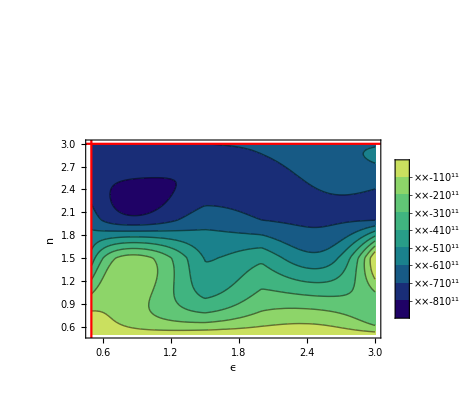

```mathematica
ab=misfit[0.3,0.9,0,1.48]
xy=Interpolation[ab]
Show[ContourPlot[xy[x,y],{x,0.5,3},{y,0.5,3},(*ContourShading->*)PlotLegends->Automatic,ColorFunction->ColorData[{"BlueGreenYellow",{0,1}}]](*,%291*),ListLinePlot[{Table[{0.5,y},{y,Range[0,5.5,0.075]}],Table[{y,3},{y,Range[00,3.05,0.001]}]},PlotStyle->{{Dashing[{0.01,1*^-2,0.01,1*^-2}],Red},{Dashing[{0.01,1*^-2,0.01,1*^-2}],Red}}],(*FrameTicks->{{{0.3,0.4,0.5,0.6,0.7,0.8,0.9},None},{{0,1,2,3,4,5},None}},*)FrameLabel->{{HoldForm[n],None},{HoldForm[ϵ],None}},LabelStyle->{FontFamily->"Times New Roman",16,GrayLevel[0]},Epilog->{Text[Style["(a)","Times New Roman",18,Black],{0.33,4.75}]}]
```

{{0.5,0.5,-2.59436×10^11},{0.5,1,-4.96498×10^12},{0.5,1.5,-1.18834×10^13},{0.5,2,-1.14963×10^13},{0.5,2.5,-9.92247×10^12},{0.5,3,-8.18969×10^12},{1,0.5,-8.64024×10^11},{1,1,-5.82316×10^12},{1,1.5,-5.41866×10^12},{1,2,-1.15413×10^13},{1,2.5,-8.27963×10^12},{1,3,-8.92032×10^12},{1.5,0.5,-5.43251×10^11},{1.5,1,-1.21681×10^13},{1.5,1.5,-1.54036×10^13},{1.5,2,-1.40267×10^13},{1.5,2.5,-8.25785×10^12},{1.5,3,-6.40024×10^12},{2,0.5,-4.39529×10^11},{2,1,-1.10176×10^13},{2,1.5,-1.40914×10^13},{2,2,-1.28822×10^13},{2,2.5,-7.90954×10^12},{2,3,-6.33083×10^12},{2.5,0.5,-6.27752×10^11},{2.5,1,-1.33331×10^13},{2.5,1.5,-1.63609×10^13},{2.5,2,-1.09797×10^13},{2.5,2.5,-9.74537×10^12},{2.5,3,-6.36634×10^12},{3,0.5,-8.97879×10^11},{3,1,-7.8333×10^12},{3,1.5,0.000508538},{3,2,-1.06353×10^13},{3,2.5,-7.52367×10^12},{3,3,-7.5986×10^12}}

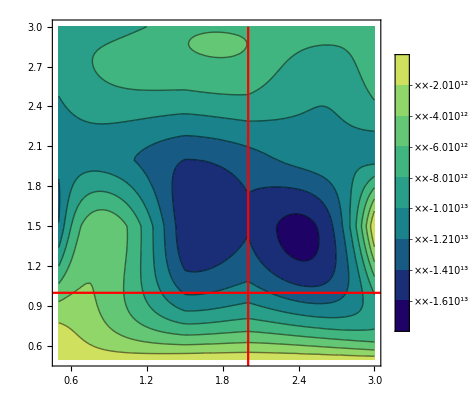

```mathematica
ab=misfit[0.3,0.9,0.9,1.48]
Show[ContourPlot[Interpolation[ab][b,y],{b,0.5,3.},{y,0.5,3.},FrameTicks->{{Automatic,None},{Automatic,None}},(*ContourShading->*)PlotLegends->Automatic,ColorFunction->ColorData[{"BlueGreenYellow",{0,1}}]],ListLinePlot[{Table[{2,y},{y,Range[0,3.05,0.075]}],Table[{y,1},{y,Range[00,3.05,0.001]}]},PlotStyle->{{Dashing[{0.01,1*^-2,0.01,1*^-2}],Red},{Dashing[{0.01,1*^-2,0.01,1*^-2}],Red}},PlotRange->{{0,7},{0,7}}]]
```

```mathematica
{{0.5,0.5,-5.056355157589321*^27},{0.5,1,-3.114720778805703*^30},{0.5,1.5,-2.822089175924144*^30},{0.5,2,-8.080372059586584*^29},{0.5,2.5,-3.017550010832966*^29},{0.5,3,-1.5033864182574542*^29},{1,0.5,-9.04584015046791*^28},{1,1,-4.541405204580547*^30},{1,1.5,-3.5022980386293357*^30},{1,2,-4.268451262133152*^29},{1,2.5,-1.3696739477339197*^29},{1,3,-1.699413662497645*^29},{1.5,0.5,-2.824878059084471*^28},{1.5,1,-3.607970047812581*^30},{1.5,1.5,-2.594316349149826*^30},{1.5,2,-8.652863028151904*^29},{1.5,2.5,-1.2704689287730796*^29},{1.5,3,-6.782559557782473*^28},{2,0.5,-1.4048904989708843*^28},{2,1,-8.033103166067595*^30},{2,1.5,-3.3124919659003354*^30},{2,2,-4.8147831606249615*^29},{2,2.5,-1.1214136602928308*^29},{2,3,-6.60397305899418*^28},{2.5,0.5,-3.3285739757550965*^28},{2.5,1,-6.946604863898371*^30},{2.5,1.5,-1.2340765165199995*^30},{2.5,2,-2.6909694348606082*^29},{2.5,2.5,-1.7017256204858347*^29},{2.5,3,-6.214644334061473*^28},{3,0.5,-7.662450533417731*^28},{3,1,-5.231609183798746*^30},{3,1.5,-1.049336389854863*^30},{3,2,-2.3295342592759278*^29},{3,2.5,-9.611455898020728*^28},{3,3,-9.280091472331176*^28}}
```

{{0.5,0.5,-5.05636×10^27},{0.5,1,-3.11472×10^30},{0.5,1.5,-2.82209×10^30},{0.5,2,-8.08037×10^29},{0.5,2.5,-3.01755×10^29},{0.5,3,-1.50339×10^29},{1,0.5,-9.04584×10^28},{1,1,-4.54141×10^30},{1,1.5,-3.5023×10^30},{1,2,-4.26845×10^29},{1,2.5,-1.36967×10^29},{1,3,-1.69941×10^29},{1.5,0.5,-2.82488×10^28},{1.5,1,-3.60797×10^30},{1.5,1.5,-2.59432×10^30},{1.5,2,-8.65286×10^29},{1.5,2.5,-1.27047×10^29},{1.5,3,-6.78256×10^28},{2,0.5,-1.40489×10^28},{2,1,-8.0331×10^30},{2,1.5,-3.31249×10^30},{2,2,-4.81478×10^29},{2,2.5,-1.12141×10^29},{2,3,-6.60397×10^28},{2.5,0.5,-3.32857×10^28},{2.5,1,-6.9466×10^30},{2.5,1.5,-1.23408×10^30},{2.5,2,-2.69097×10^29},{2.5,2.5,-1.70173×10^29},{2.5,3,-6.21464×10^28},{3,0.5,-7.66245×10^28},{3,1,-5.23161×10^30},{3,1.5,-1.04934×10^30},{3,2,-2.32953×10^29},{3,2.5,-9.61146×10^28},{3,3,-9.28009×10^28}}

```mathematica
Transpose[Join[{Transpose[%56][[1]]},{Transpose[%56][[2]]},{Transpose[%56][[3]]/10^30}]]
```

{{0.5,0.5,-0.00505636},{0.5,1,-3.11472},{0.5,1.5,-2.82209},{0.5,2,-0.808037},{0.5,2.5,-0.301755},{0.5,3,-0.150339},{1,0.5,-0.0904584},{1,1,-4.54141},{1,1.5,-3.5023},{1,2,-0.426845},{1,2.5,-0.136967},{1,3,-0.169941},{1.5,0.5,-0.0282488},{1.5,1,-3.60797},{1.5,1.5,-2.59432},{1.5,2,-0.865286},{1.5,2.5,-0.127047},{1.5,3,-0.0678256},{2,0.5,-0.0140489},{2,1,-8.0331},{2,1.5,-3.31249},{2,2,-0.481478},{2,2.5,-0.112141},{2,3,-0.0660397},{2.5,0.5,-0.0332857},{2.5,1,-6.9466},{2.5,1.5,-1.23408},{2.5,2,-0.269097},{2.5,2.5,-0.170173},{2.5,3,-0.0621464},{3,0.5,-0.0766245},{3,1,-5.23161},{3,1.5,-1.04934},{3,2,-0.232953},{3,2.5,-0.0961146},{3,3,-0.0928009}}

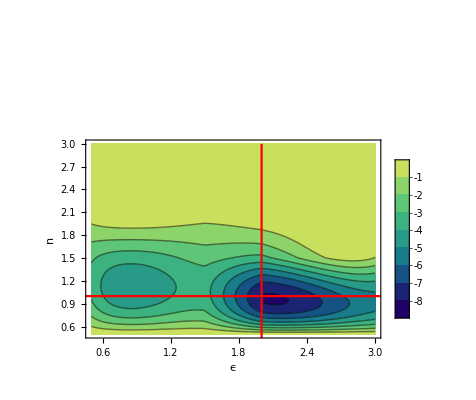

```mathematica
Show[ContourPlot[Interpolation[%70][b,y],{b,0.5,3.},{y,0.5,3.},FrameTicks->{{Automatic,None},{Automatic,None}},(*ContourShading->*)PlotLegends->Automatic,ColorFunction->ColorData[{"BlueGreenYellow",{0,1}}]],ListLinePlot[{Table[{2,y},{y,Range[0,3.05,0.075]}],Table[{y,1},{y,Range[00,3.05,0.001]}]},PlotStyle->{{Dashing[{0.01,1*^-2,0.01,1*^-2}],Red},{Dashing[{0.01,1*^-2,0.01,1*^-2}],Red}}],FrameLabel->{{HoldForm[n],None},{HoldForm[ϵ],None}},LabelStyle->{FontFamily->"Times New Roman",16,GrayLevel[0]},Epilog->{Text[Style["(a)","Times New Roman",18,Black],{0.33,4.75}]}]
```

```mathematica
Export["fig_3_2.pdf",%73]
```

fig_3_2.pdf

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["fig_3_2.pdf"]]]
```

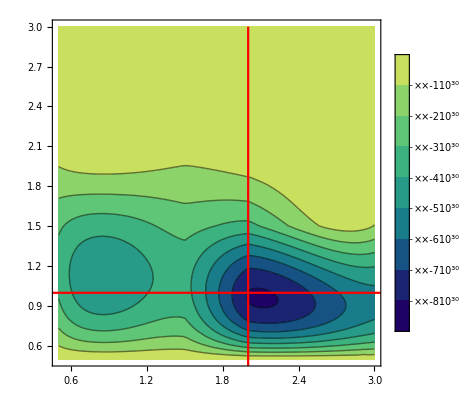

```mathematica
Show[ContourPlot[Interpolation[%56][b,y],{b,0.5,3.},{y,0.5,3.},FrameTicks->{{Automatic,None},{Automatic,None}},(*ContourShading->*)PlotLegends->Automatic,ColorFunction->ColorData[{"BlueGreenYellow",{0,1}}]],ListLinePlot[{Table[{2,y},{y,Range[0,3.05,0.075]}],Table[{y,1},{y,Range[00,3.05,0.001]}]},PlotStyle->{{Dashing[{0.01,1*^-2,0.01,1*^-2}],Red},{Dashing[{0.01,1*^-2,0.01,1*^-2}],Red}},PlotRange->{{0,7},{0,7}}]]
```

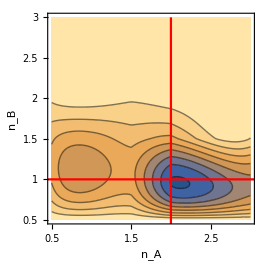

```mathematica
%49
```

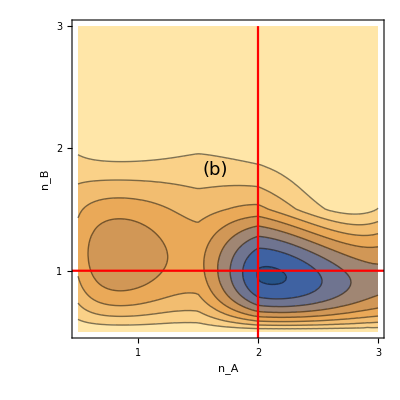

```mathematica
Show[ContourPlot[Interpolation[%293][b,y],{b,0.5,3.},{y,0.5,3.}],ListLinePlot[{Table[{2,y},{y,Range[0,3.05,0.075]}],Table[{y,1},{y,Range[00,3.05,0.001]}]},PlotStyle->{{Dashing[{0.01,1*^-2,0.01,1*^-2}],Red},{Dashing[{0.01,1*^-2,0.01,1*^-2}],Red}}],FrameTicks->{{{0,1,2,3},None},{{0,1,2,3},None}},FrameLabel->{{HoldForm[Subscript[n, B]],None},{HoldForm[Subscript[n, A]],None}},LabelStyle->{FontFamily->"Times New Roman",16,GrayLevel[0]},Epilog->{Text[Style["(b)","Times New Roman"
,18],Scaled[{0.5,0.5}],{12.7,-13.5}]}]
```

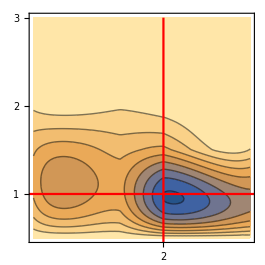

-Graphics-

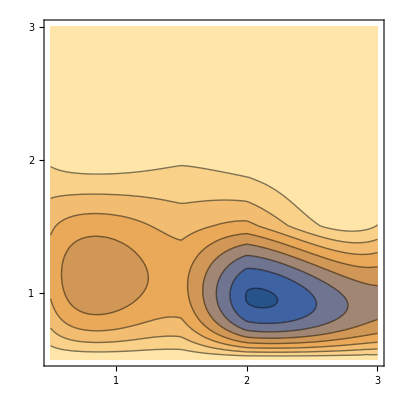

```mathematica
ContourPlot[Interpolation[%49][b,y],{b,0.5,3.},{y,0.5,3.},FrameTicks->{{{0,1,2,3},None},{{0,1,2,3},None}}]
```

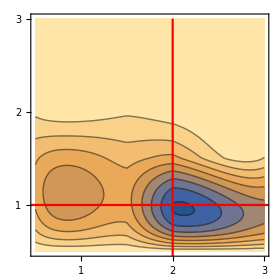

-Graphics-

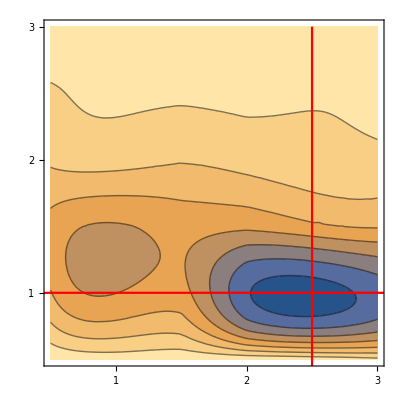

```mathematica
Show[ContourPlot[Interpolation[ab][b,y],{b,0.5,3.},{y,0.5,3.},FrameTicks->{{{0,1,2,3},None},{{0,1,2,3},None}}],ListLinePlot[{Table[{2.5,y},{y,Range[0,3.05,0.075]}],Table[{y,1},{y,Range[00,3.05,0.001]}]},PlotStyle->{{Dashing[{0.01,1*^-2,0.01,1*^-2}],Red},{Dashing[{0.01,1*^-2,0.01,1*^-2}],Red}},PlotRange->{{0,7},{0,7}}]]
```

```mathematica
%101
```

```mathematica
{{0.5,0.5,-6.329988592242464},{0.5,1,-7.3877991570072705},{0.5,1.5,-7.207495585498011},{0.5,2,-6.9222342646449855},{0.5,2.5,-6.739714949069516},{0.5,3,-6.610779142392051},{1,0.5,-6.862930639178895},{1,1,-7.488276855567408},{1,1.5,-7.426855998694049},{1,2,-6.820673327801062},{1,2.5,-6.602266951401239},{1,3,-6.633490215298203},{1.5,0.5,-6.66673146157731},{1.5,1,-7.2361162694993215},{1.5,1.5,-7.178684972071807},{1.5,2,-6.938355087829402},{1.5,2.5,-6.588521002950826},{1.5,3,-6.476002671445956},{2,0.5,-6.5201130333360044},{2,1,-7.527418183812744},{2,1.5,-7.21894888473275},{2,2,-6.836651285791599},{2,2.5,-6.573856043467242},{2,3,-6.468638647585809},{2.5,0.5,-6.677622105097013},{2.5,1,-7.496444238017934},{2.5,1.5,-7.039298282798969},{2.5,2,-6.734443475452641},{2.5,2.5,-6.641636732457223},{2.5,3,-6.459556261173884},{3,0.5,-6.833082425028125},{3,1,-7.4400349638863705},{3,1.5,-6.999975406391379},{3,2,-6.712016213116248},{3,2.5,-6.5406049509492235},{3,3,-6.5292933137029445}}
```

{{0.5,0.5,-6.32999},{0.5,1,-7.3878},{0.5,1.5,-7.2075},{0.5,2,-6.92223},{0.5,2.5,-6.73971},{0.5,3,-6.61078},{1,0.5,-6.86293},{1,1,-7.48828},{1,1.5,-7.42686},{1,2,-6.82067},{1,2.5,-6.60227},{1,3,-6.63349},{1.5,0.5,-6.66673},{1.5,1,-7.23612},{1.5,1.5,-7.17868},{1.5,2,-6.93836},{1.5,2.5,-6.58852},{1.5,3,-6.476},{2,0.5,-6.52011},{2,1,-7.52742},{2,1.5,-7.21895},{2,2,-6.83665},{2,2.5,-6.57386},{2,3,-6.46864},{2.5,0.5,-6.67762},{2.5,1,-7.49644},{2.5,1.5,-7.0393},{2.5,2,-6.73444},{2.5,2.5,-6.64164},{2.5,3,-6.45956},{3,0.5,-6.83308},{3,1,-7.44003},{3,1.5,-6.99998},{3,2,-6.71202},{3,2.5,-6.5406},{3,3,-6.52929}}

```mathematica
Transpose[Join[{Transpose[%24][[1]]},{Transpose[%24][[2]]},{-Transpose[%24][[3]]}]]
```

{{0.5,0.5,6.32999},{0.5,1,7.3878},{0.5,1.5,7.2075},{0.5,2,6.92223},{0.5,2.5,6.73971},{0.5,3,6.61078},{1,0.5,6.86293},{1,1,7.48828},{1,1.5,7.42686},{1,2,6.82067},{1,2.5,6.60227},{1,3,6.63349},{1.5,0.5,6.66673},{1.5,1,7.23612},{1.5,1.5,7.17868},{1.5,2,6.93836},{1.5,2.5,6.58852},{1.5,3,6.476},{2,0.5,6.52011},{2,1,7.52742},{2,1.5,7.21895},{2,2,6.83665},{2,2.5,6.57386},{2,3,6.46864},{2.5,0.5,6.67762},{2.5,1,7.49644},{2.5,1.5,7.0393},{2.5,2,6.73444},{2.5,2.5,6.64164},{2.5,3,6.45956},{3,0.5,6.83308},{3,1,7.44003},{3,1.5,6.99998},{3,2,6.71202},{3,2.5,6.5406},{3,3,6.52929}}

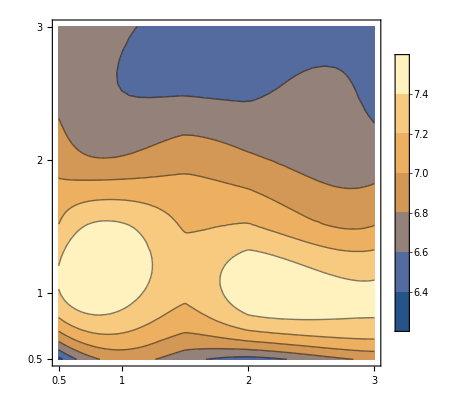

```mathematica
ContourPlot[Interpolation[%39][b,y],{b,0.5,3.},{y,0.5,3.},FrameTicks->{{{0.5,1,2,3},None},{{0.5,1,2,3},None}},PlotLegends->Automatic,LabelStyle->{FontFamily->"Times New Roman",16,GrayLevel[0]}]
```

```mathematica
%29[[2]]
```

Placed[,After,Identity]

```mathematica
Position[ab,Min[ab]][[1,1]]
```

32

```mathematica
{ab[[Position[ab,Min[ab]][[1,1]],1]],ab[[Position[ab,Min[ab]][[1,1]],2]]}
```

{2.5,1}

```mathematica
Show[%133,FrameTicks->{{{0,0.5,1,1.5,2,2.5,3},None},{{0,0.5,1,1.5,2,2.5,3},None}}]
```

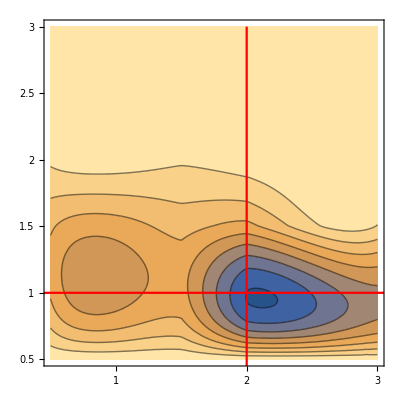
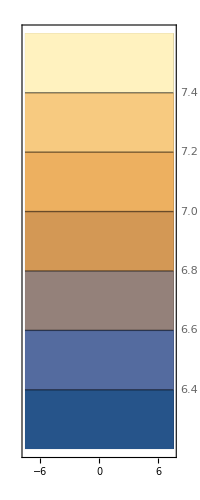

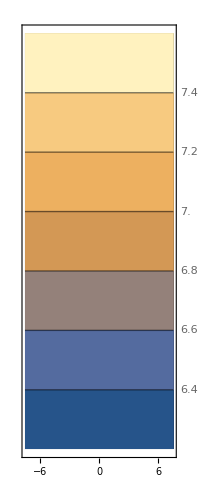
-Graphics- -Graphics-

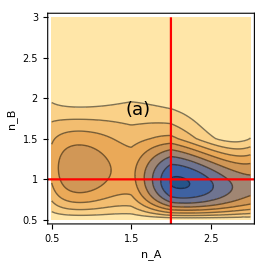
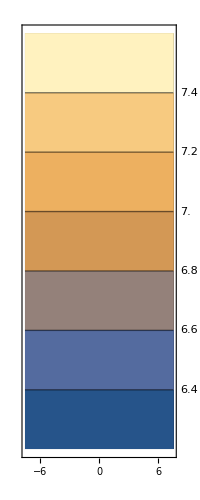

```mathematica
Row[{Show[%18,FrameLabel->{{HoldForm[Subscript[n, B]],None},{HoldForm[Subscript[n, A]],None}},FrameTicks->{{{0.5,1,1.5,2,2.5,3},None},{{0.5,1,1.5,2,2.5,3},None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",16,GrayLevel[0]},Epilog->{Text[Style["(a)","Times New Roman"
,18],Scaled[{0.5,0.5}],{12,-12}]}],%62}]
```

```mathematica
Row[{%88,%62}]
```

```mathematica
Export["example3.pdf",%90]
```

example3.pdf

```mathematica
SystemOpen["example3.pdf"]
```

-Graphics-

```mathematica
Show[%49,PlotLabel->None]
```

-Graphics-

```mathematica
Show[%52]
```

-Graphics-

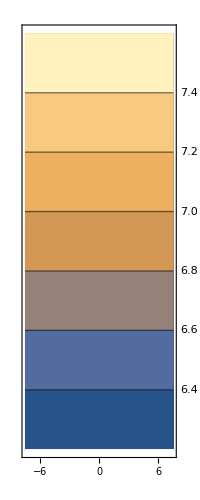

-Graphics-

```mathematica
Show[]
```

```mathematica
Export["example2.pdf",%62]
```

example2.pdf

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["example2.pdf"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["example.pdf"]]]
```

```mathematica
SystemOpen["example.pdf"]
```

```mathematica
{{0,0,-3.6353278964719945*^8},{1,1,-3.6639905659462417*^352},{1,2,-7.609357069730656*^351},{1,3,-4.488497226751244*^351},{2,1,-3.2593405274658716*^352},{2,2,-8.036424185526595*^351},{2,3,-2.7889830027100696*^351},{3,1,-3.127223906197367*^352},{3,2,-5.700522148456101*^351},{3,3,-3.3663842475892725*^351},{0,1,-2.74956853626894*^352},{0,2,-9.56144064515556*^351},{0,3,-3.505737398347799*^351},{1,0,-2.6846160260907598*^9},{2,0,-1.046919656915527*^350},{3,0,-3.167907868488863*^350}}
```

{{0,0,-3.63533×10^8},{1,1,-3.66399×10^12},{1,2,-7.60936×10^11},{1,3,-4.4885×10^11},{2,1,-3.25934×10^12},{2,2,-8.03642×10^11},{2,3,-2.78898×10^11},{3,1,-3.12722×10^12},{3,2,-5.70052×10^11},{3,3,-3.36638×10^11},{0,1,-2.74957×10^12},{0,2,-9.56144×10^11},{0,3,-3.50574×10^11},{1,0,-2.68462×10^9},{2,0,-1.04692×10^10},{3,0,-3.16791×10^10}}

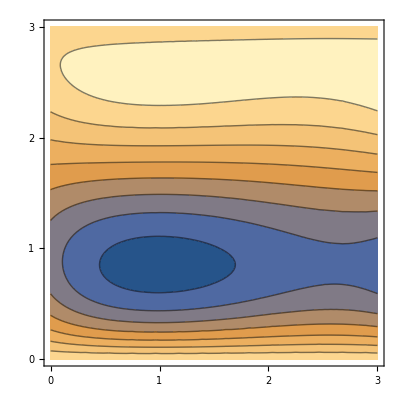

```mathematica
ContourPlot[Interpolation[%18][z,y],{z,0,3.},{y,0,3.},FrameTicks->{{{0,1,2,3},None},{{0,1,2,3},None}}]
```

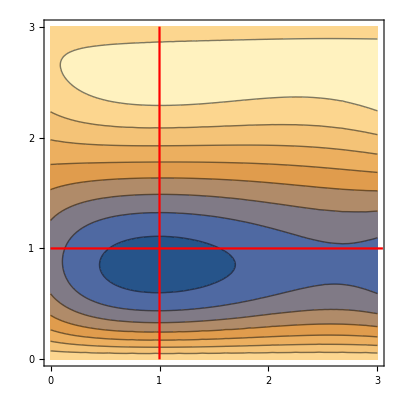

```mathematica
Show[%29,ListLinePlot[{Table[{1,y},{y,Range[0,3.05,0.075]}],Table[{y,1},{y,Range[00,3.05,0.001]}]},PlotStyle->{{Dashing[{0.01,1*^-2,0.01,1*^-2}],Red},{Dashing[{0.01,1*^-2,0.01,1*^-2}],Red}},PlotRange->{{0,7},{0,7}}]]
```

```mathematica
Show[%30,FrameLabel->{{HoldForm[Subscript[n, B]],None},{HoldForm[Subscript[n, A]],None}},PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->{520,520}]
```

-Graphics-

```mathematica
Show[%198,ImageSize->{540,540}]
```

-Graphics-

-Graphics--Graphics-

```mathematica
Show[%365,FrameLabel->{{HoldForm[n],None},{HoldForm[ϵ],None}},PlotLabel->None,LabelStyle->{FontFamily->"Arial",17,GrayLevel[0]},ImageSize->{500,500}]
```

-Graphics-

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2 π},PlotStyle->{Thickness[0.01],Thickness[0.02]}]
```

-Graphics-

```mathematica
aa=misfit[0.3,0.9,0.5,0,1.49]
bb1=Sort[Join[aa[[1]],aa[[2]],aa[[3]],aa[[4]],aa[[5]],aa[[6]],aa[[7]]]]
bb2=Sort[Join[aa[[7]],aa[[8]],aa[[9]],aa[[10]],aa[[11]],aa[[12]]]]
ListContourPlot[bb1,PlotRange->{{0,3},{0,3}}]
(*ContourPlot[ListInterpolation[bb1][x,y],{x,0,3},{y,0,3}]*)
```

{{{2,0,-5.98938},{1.4,0.6,-6.08716},{1,1,-6.06398},{0.6,1.4,-5.77775},{0,2,-4.62204}},{{3,0,-5.84049},{2,1,-5.97847},{1.5,1.5,-6.09995},{1,2,-6.09946},{0,3,-4.96636}},{{3,1,-5.84405},{2,2,-5.9835},{1,3,-6.14618}},{{0,0,-3.71566}},{{2.5,2.5,-5.87743}},{{3,3,-5.79764}},{{1,0,-5.87408},{0.7,0.3,-5.69622},{0.5,0.5,-5.43042},{0.3,0.7,-5.03307},{0,1,-4.23198}},{{0.3,1,-4.33925},{0.4,1,-4.70725},{0.5,1,-5.12989},{0.6,1,-5.53624},{0.7,1,-5.87612},{0.8,1,-6.09184},{0.9,1,-6.18048}},{{0.3,2,-4.74968},{0.4,2,-5.37929},{0.5,2,-5.98821},{0.6,2,-6.32568},{0.7,2,-6.32328},{0.8,2,-6.12918},{0.9,2,-5.93554}},{{0.3,3,-5.11534},{0.4,3,-5.90483},{0.5,3,-6.38091},{0.6,3,-6.29108},{0.7,3,-6.02627},{0.8,3,-5.79324},{0.9,3,-5.63817}},{{0.3,4,-5.44313},{0.4,4,-6.25646},{0.5,4,-6.32927},{0.6,4,-6.02508},{0.7,4,-5.749},{0.8,4,-5.58065},{0.9,4,-5.47667}},{{0.3,5,-5.72111},{0.4,5,-6.3796},{0.5,5,-6.12037},{0.6,5,-5.82151},{0.7,5,-5.59188},{0.8,5,-5.4645},{0.9,5,-5.39311}},{{0.3,6,-5.94743},{0.4,6,-6.37786},{0.5,6,-5.93959},{0.6,6,-5.67081},{0.7,6,-5.49314},{0.8,6,-5.39761},{0.9,6,-5.34927}}}

{{0,0,-3.71566},{0,1,-4.23198},{0,2,-4.62204},{0,3,-4.96636},{0.3,0.7,-5.03307},{0.5,0.5,-5.43042},{0.6,1.4,-5.77775},{0.7,0.3,-5.69622},{1,0,-5.87408},{1,1,-6.06398},{1,2,-6.09946},{1,3,-6.14618},{1.4,0.6,-6.08716},{1.5,1.5,-6.09995},{2,0,-5.98938},{2,1,-5.97847},{2,2,-5.9835},{2.5,2.5,-5.87743},{3,0,-5.84049},{3,1,-5.84405},{3,3,-5.79764}}

{{0,1,-4.23198},{0.3,0.7,-5.03307},{0.3,1,-4.33925},{0.3,2,-4.74968},{0.3,3,-5.11534},{0.3,4,-5.44313},{0.3,5,-5.72111},{0.4,1,-4.70725},{0.4,2,-5.37929},{0.4,3,-5.90483},{0.4,4,-6.25646},{0.4,5,-6.3796},{0.5,0.5,-5.43042},{0.5,1,-5.12989},{0.5,2,-5.98821},{0.5,3,-6.38091},{0.5,4,-6.32927},{0.5,5,-6.12037},{0.6,1,-5.53624},{0.6,2,-6.32568},{0.6,3,-6.29108},{0.6,4,-6.02508},{0.6,5,-5.82151},{0.7,0.3,-5.69622},{0.7,1,-5.87612},{0.7,2,-6.32328},{0.7,3,-6.02627},{0.7,4,-5.749},{0.7,5,-5.59188},{0.8,1,-6.09184},{0.8,2,-6.12918},{0.8,3,-5.79324},{0.8,4,-5.58065},{0.8,5,-5.4645},{0.9,1,-6.18048},{0.9,2,-5.93554},{0.9,3,-5.63817},{0.9,4,-5.47667},{0.9,5,-5.39311},{1,0,-5.87408}}

-Graphics-